## RR Geometry

```mathematica
(* Set up code to make arrows *)
```

```mathematica
r1Vec[r1_] := Arrow[{{0,0}, {0,r1}}];
r2Vec[r2_, costh_]:= Module[{sinth}, 
sinth = Sqrt[1-costh^2];
Arrow[{{0,0},{r2*sinth, r2*costh}}]
];
slVec[r1_, r2_ ,costh_]:= Module[{sinth},
sinth = Sqrt[1-costh^2];
{Dashed, Arrow[{{0,r1}, {r2*sinth, r2*costh}}],Arrow[{{0,0},{r2*sinth/2, (r1+r2*costh)/2}}]}
];
```

```mathematica
drawVecs[r1_, r2_, costh_]:= Graphics[{r1Vec[r1], r2Vec[r2, costh], slVec[r1,r2,costh]}];
```

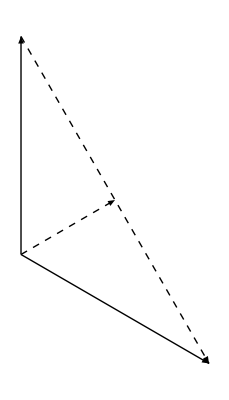

```mathematica
drawVecs[1.0, 1.0, -0.5]
```

```mathematica
(* Solve quadratic for l, keep only real roots *)
```

```mathematica
goodRoots[l1_]:= Module[ {},
(Element[l, Reals] && (l ≥ 0))/.l1
];
```

```mathematica
lSolveFull[s_, μ_, r1_] := NSolve[l^2+s l μ + s^2/4- r1^2 == 0, l];
```

```mathematica
lSolve[s_, μ_, r1_]:=Select[lSolveFull[s,μ,r1] , goodRoots];
```

```mathematica
r2Solve[s_, l_, r1_] := Sqrt[(s^2+4 l^2-2 r1^2)/2];
```

```mathematica
costhSolve[s_, r1_,r2_]:= (r1^2+r2^2-s^2)/(2 r1 r2);
```

```mathematica
drawFunc[s_,μ_]:=Module[{r2,costh,l1},
l1=(l/.lSolve[s,μ,1])[[1]];
r2 = r2Solve[s,l1, 1];
costh = costhSolve[s,1,r2];
drawVecs[1.0, r2, costh]
];
```

```mathematica
Manipulate[drawFunc[s, μ], {s,0.01,1.5}, {μ,-0.9,0.9}]
```

## Jacobian

```mathematica
(* Let us derive an expression for mu in terms of r1, r2, and costh = λ *)
x1 = {0, r1}
x2 = {r2 Sqrt[1-λ^2], r2 λ}
```

{0,r1}

{r2 √(1-λ^2),r2 λ}

```mathematica
svec = x1-x2
lvec = (x1+x2)/2
```

{-r2 √(1-λ^2),r1-r2 λ}

{1/2 r2 √(1-λ^2),1/2 (r1+r2 λ)}

```mathematica
muFunc[r1_, r2_, λ_]:=Simplify[(svec.lvec)/(Norm[svec] Norm[lvec]), r1>0 && r2>0 && λ ≥ -1 && λ ≤ 1]
```

```mathematica
muFunc[r1, r2, λ]
```

(r1^2-r2^2)/(√(r1^4+r2^4+2 r1^2 r2^2 (1-2 λ^2)))

```mathematica
sFunc[r1_,r2_, λ_]:=Simplify[Norm[svec],  r1>0 && r2>0 && λ ≥ -1 && λ ≤ 1]
```

```mathematica
sFunc[r1,r2,λ]
```

√(r1^2+r2^2-2 r1 r2 λ)

```mathematica
jMat[r1_,r2_,λ_]:=Simplify[D[{sFunc[r1,r2,λ], muFunc[r1,r2,λ]},{{r2,λ}}], r1>0 && r2>0 && λ ≥ -1 && λ ≤ 1]
```

```mathematica
jMat[r1,r2,λ]
```

{{(r2-r1 λ)/(√(r1^2+r2^2-2 r1 r2 λ)),-(r1 r2)/(√(r1^2+r2^2-2 r1 r2 λ))},{(4 r1^2 r2 (r1^2+r2^2) (-1+λ^2))/((r1^4+r2^4+2 r1^2 r2^2 (1-2 λ^2))^(3/2)),(4 r1^2 r2^2 (r1^2-r2^2) λ)/((r1^4+r2^4+2 r1^2 r2^2 (1-2 λ^2))^(3/2))}}

```mathematica
Simplify[Det[jMat[r1,r2,λ]],r1>0 && r2>0 && λ ≥ -1 && λ ≤ 1]
```

-(4 r1^2 r2^2 (r1+r2 λ))/((r1^2+r2^2-2 r1 r2 λ) (r1^2+r2^2+2 r1 r2 λ)^(3/2))

## Shell RR

```mathematica
(* Define a generic normalized constant density function *)
```

```mathematica
vol[rmin_, rmax_]:= (rmax^3- rmin^3)/3;
```

```mathematica
nFunc[r_,rmin_,rmax_]:=Piecewise[{{1/vol[rmin,rmax],(r >= rmin) &&(r≤ rmax)}}];
```

```mathematica
(* Test the normalization *)
```

```mathematica
Integrate[r^2 nFunc[r, 500.0,1000.0], {r, 0, Infinity}]
```

1.

```mathematica
(* Write a wrapper r2 function that takes in r, μ and r1 and returns r2 *)
```

```mathematica
r2Func[s_,μ_,r1_] := Module[{l1}, 
Sow[r1];
l1=(l/.lSolve[s,μ,r1])[[1]];
r2Solve[s,l1, r1]
];
```

## Example

```mathematica
(* Define a simple number density function *)
n1[r_] := nFunc[r, 500.0, 2000.0];
```

```mathematica
(* Integrand *)
RRint[r1_?NumericQ,s_, μ_] := Module[{r2},
r2 = r2Func[s,μ,r1];
r1^2 n1[r1] r2^2 n1[r2]
];
```